Most mezi ostrovy

```mathematica
g1[x_, y_] := x^2 + (5*(y - 3)/4 - Sqrt[Abs[x]])^2
```

```mathematica
g2[x_, y_] := (2*(x - 3)^2 + 2*(y - 4)^2 )^3  - 40*(x - 3)^2 * (y - 4)^2
```

```mathematica
ostrov1 := g1[x,y]≤ 1
```

```mathematica
ostrov2 := g2[x,y]≤ 1
```

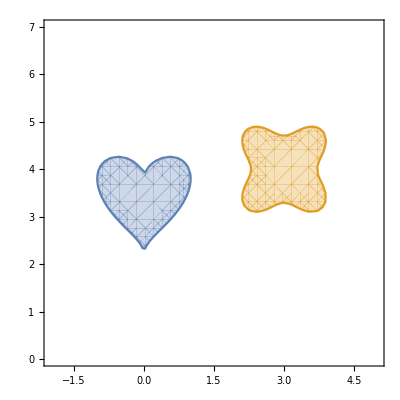

```mathematica
map = RegionPlot[{ostrov1, ostrov2},{x,-2,5},{y,0,7}]
```

```mathematica
dobrobod = {0.9890868254063674,3.6777760374835426}
amebod = {2.1115482359957065,3.483334993036259}
```

{0.989087,3.67778}

{2.11155,3.48333}

```mathematica
{2.1115482359957065,3.483334993036259}
```

{2.11155,3.48333}

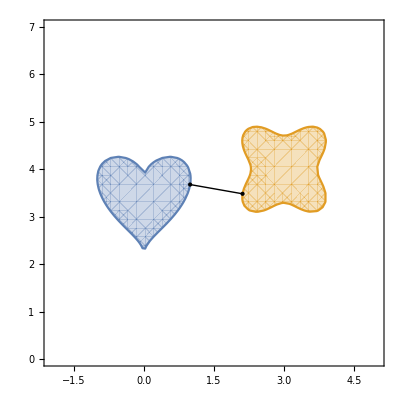

```mathematica
Show[map, Graphics[Point[dobrobod]], Graphics[Point[amebod]], Graphics[Line[{dobrobod, amebod}]]]
```